```mathematica
Table[x* y^n,{n,12}]
D[%,y]
```

{x y,x y^2,x y^3,x y^4,x y^5,x y^6,x y^7,x y^8,x y^9,x y^10,x y^11,x y^12}

{x,2 x y,3 x y^2,4 x y^3,5 x y^4,6 x y^5,7 x y^6,8 x y^7,9 x y^8,10 x y^9,11 x y^10,12 x y^11}

```mathematica
Sin[{a,2d,c}]
```

{Sin[a],Sin[2 d],Sin[c]}

```mathematica
Sqrt[{12,3,4}]
```

{2 √3,√3,2}

```mathematica
T={15,20,25,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,298.1};
Cp={0.311,0.605,0.858,1.075,1.452,1.772,2.084,2.352,2.604,2.838,3.060,3.254,3.445,3.624,3.795,3.964,4.123,4.269,4.404,4.526,4.639,4.743,4.841,4.927,5.010,5.083,5.154,5.220,5.286,5.350,5.401};
CpoverT=Cp/T
```

{0.0207333,0.03025,0.03432,0.0358333,0.0363,0.03544,0.0347333,0.0336,0.03255,0.0315333,0.0306,0.0295818,0.0287083,0.0278769,0.0271071,0.0264267,0.0257688,0.0251118,0.0244667,0.0238211,0.023195,0.0225857,0.0220045,0.0214217,0.020875,0.020332,0.0198231,0.0193333,0.0188786,0.0184483,0.0181181}

```mathematica
Sum[(CpoverT[[i+1]]+CpoverT[[i]])((T[[i+1]]-T[[i]])/2),{i,Length[T]-1}]//N
```

7.50452

```mathematica
Transpose[{T,Cp}]
```

{{15,0.311},{20,0.605},{25,0.858},{30,1.075},{40,1.452},{50,1.772},{60,2.084},{70,2.352},{80,2.604},{90,2.838},{100,3.06},{110,3.254},{120,3.445},{130,3.624},{140,3.795},{150,3.964},{160,4.123},{170,4.269},{180,4.404},{190,4.526},{200,4.639},{210,4.743},{220,4.841},{230,4.927},{240,5.01},{250,5.083},{260,5.154},{270,5.22},{280,5.286},{290,5.35},{298.1,5.401}}

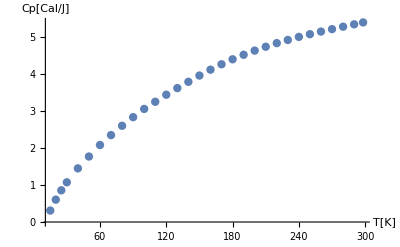

```mathematica
ListPlot[%,PlotStyle->PointSize[0.015],AxesLabel->{"T[K]","Cp[Cal/J]"},PlotRange->All]
```

```mathematica
ϵ[n_]:=(n+ 1/2) ℏ*ω;(* se usa ': Comad' que es la tecla Esc que tiene su equivalente \[Comand] para escribir otro pipo de caracteres *)
```

```mathematica
ϵ[5]
```

(11 ω ℏ)/2

### Programing

```mathematica
(*Si la expresion es atomica (indivisible) retorna True*)??AtomQ
```

RowBox[{"AtomQ", "[", StyleBox["expr", "TI"], "]"}] yields True if StyleBox["expr", "TI"] is an expression which cannot be divided into subexpressions, and yields False otherwise.

Attributes[AtomQ]={Protected}

```mathematica
Head[I+2]
Head[Sqrt[2]]
Head[x.b2]
Head[2^32]
Head[1/3]
```

Complex

Power

Symbol

Integer

Rational

```mathematica
??FullForm
```

RowBox[{"FullForm", "[", StyleBox["expr", "TI"], "]"}] prints as the full form of StyleBox["expr", "TI"], with no special syntax.

Attributes[FullForm]={Protected}
 
Options[FullForm]={NumberMarks:>True}

```mathematica
FullForm[Sin[x]+x+t]
```

Plus[t,x,Sin[x]]

```mathematica
Plot3D[t+x+Sin[x],{t,-8,8},{x,-8,8}]
```

-Graphics3D-

```mathematica
FullForm[x+y== 12]
```

Equal[Plus[x,y],12]

```mathematica
FullForm[z->2]
```

Rule[z,2]

```mathematica
z/.z->2
```

2

```mathematica
FullForm[a+2(s+2)^t]
```

Plus[a,Times[2,Power[Plus[2,s],t]]]

```mathematica
Power[Plus[2,s],t]
```

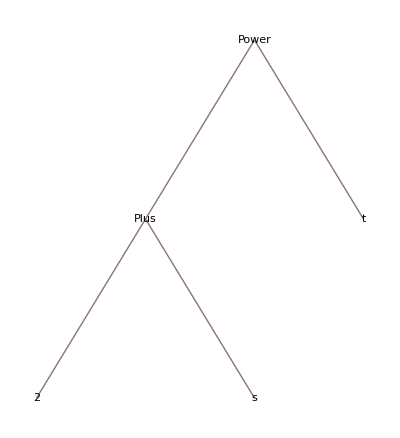

```mathematica
TreeForm[(2+s)^t]
```

## Graficas

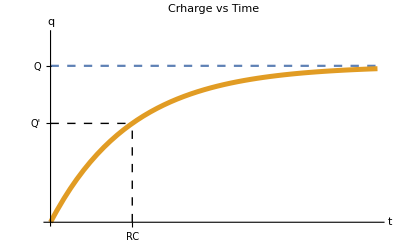

```mathematica
Plot[{1,1-E^-t},{t,0,4},PlotRange->{0,1.2},PlotStyle->{Dashing[{.015,.015}],Thickness[.009]},AxesLabel->{"t","q"},PlotLabel->"Crharge vs Time",Ticks->{{{1,"RC"}},{{.632,"Q'"},{1,"Q"}}},Epilog->{Dashing[{.015,.015}],Line[{{1,0},{1,0.632}}],Line[{{0,0.632},{1,0.632}}]}]
```

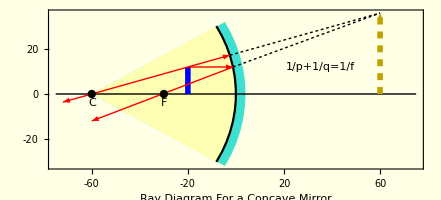

```mathematica
gr1={{RGBColor[0.25099,0.87839,0.815699],Tooltip[Disk[{-60,0},64,{2Pi -Pi/6,2Pi+Pi/6}],"mirror"]},{Lighter[Yellow,.7],Tooltip[Disk[{-60,0},60,{2Pi -Pi/6 -.005,2Pi+Pi/6 +.005}],"None",ActionDelay->999]},{Thickness[.004],Tooltip[Circle[{-60,0},60,{2Pi -Pi/6 -.004,2Pi+Pi/6 +.004}],"mirror"]}};

gr2=Tooltip[Line[{{-75,0},{75,0}}],"Principal Axis"];

gr3={Thickness[.01],{Blue,Tooltip[Arrow[{{-20,0},{-20,12}}],"Object"]},{Dashed,Darker[RGBColor[1,.8431,0],.25],Tooltip[Arrow[{{60,0},{60,36}}],"Image"]}};

gr4={{Arrowheads[{{.03,.75}}],Red,Tooltip[Arrow[{{-20,12},{-60*(1-Cos[α]),60*Sin[α]}}],"Incident Ray"]},{Red,Tooltip[Arrow[{{-20,12},{-72,-12Tan[α]}}],"Reflected Ray"]},{Arrowheads[{{.03,.75}}],Red,Tooltip[Arrow[{{-20,12},{-δ,12}}],"Incident Ray"]},{Red,Tooltip[Arrow[{{-δ,12},{-60,-30Tan[β]}}],"Reflected Ray"]}}/.{α->ArcTan[36/120],β->ArcTan[36/90],δ->60-Sqrt[60^2 -12^2]};

gr5={{Dashing[.005],Tooltip[Line[{{-60*(1-Cos[α]),60Sin[α]},{60,36}}],"Aparent Part of Reflect Ray"]},{Dashing[.005],Tooltip[Line[{{-δ,12},{60,36}}],"Aparent Part of Reflect Ray"]}}/.{α->ArcTan[36/120],δ->60-Sqrt[60^2 -12^2]};

gr6={{PointSize[.015],Tooltip[Point[{-60,0}],"Center of Curvature"],Tooltip[Point[{-30,0}],"Focal Point"]},Tooltip[Text[C,{-60,-2},{0,1}],"Center of Curvature"],Tooltip[Text[F,{-30,-2},{0,1}],"Focal Point"]};

gr7={Tooltip[Inset["1/p+1/q=1/f",{35,12}],"Mirror Equation"]};




Graphics[{gr1,gr2,gr3,gr4,gr5,gr6,gr7},BaseStyle->FontFamily->"Times New Roman",Frame->True,FrameLabel->"Ray Diagram For a Concave Mirror",FrameTicks->{Table[i,{i,-60,60,20}],{-20,0,20},None,None},PlotRangePadding->4,Background->Lighter[Yellow, 0.9] ]
```

```mathematica
ListAnimate[Table[Show[Plot[Sin[x-i*(2*Pi/8)],{x,-4*Pi,4Pi}],Graphics[{{Blue,Dashed,Line[{{0,-1},{0,1}}]},PointSize[0.03],Red,Point[{0,Sin[-i*(2*Pi/8)]}]}],Frame->True,PlotRangePadding->{None,0.2}],{i,0,7}]]
```

### Aplications

#### Mechanics

```mathematica
ClearAll["Global`*"]
```

```mathematica
DSolve[{x'[t]==v[t],v'[t]==-g-(b v[t])/m,x[0]==h,v[0]==Subscript[v, 0]},{x[t],v[t]},t]
```

```mathematica
DSolveValue[{x'[t]==v[t],v'[t]==-g-b*v[t]/m,x[0]==h,v[0]==v0},{x[t],v[t]},t]//FullSimplify
```

{(b^2 h+g m^2-b g m t+b m v0-ⅇ^(-(b t)/m) m (g m+b v0))/b^2,(-g m+ⅇ^(-(b t)/m) (g m+b v0))/b}

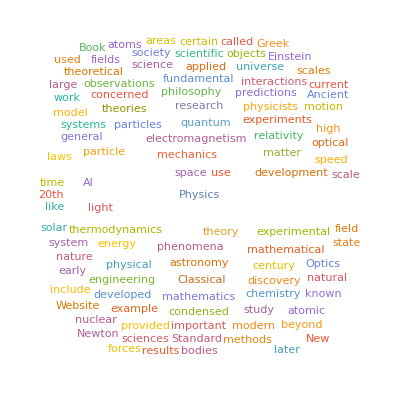

```mathematica
WordCloud[DeleteStopwords[WikipediaData["Physics"]]]
```

México

WolframAlphaQueryResults

England

WolframAlphaQueryResults